STM image (Siesta tip position centered at image):

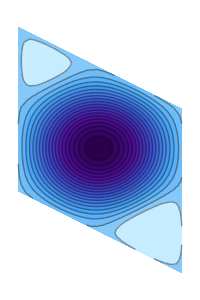

Minimum conductance: 0.030038 nA/V

Maximum conductance: 0.0589606 nA/V

Min/max ratio      : 0.50946

```mathematica
ClearAll["Global`*"]
system="/CuCO3x3/1x1/";
tmp=Import[NotebookDirectory[]<>system<>"STMimage.nc","Data"];
STMimage=tmp[[1]];theta=tmp[[2]];
Nx=Length@STMimage[[;;,1]];Ny=Length@STMimage[[1,;;]];

Print["STM image (Siesta tip position centered at image):"]
A={{1,-Cos[theta]},{0,1}};
matTransf=Table[{A[[2]].{ii,jj},A[[1]].{ii,jj},STMimage[[ii,Ny+1-jj]]},{ii,1,Nx},{jj,1,Ny}];
Rotate[ListContourPlot[Flatten[matTransf,{1,2}],AspectRatio->1+Cos[theta],PlotRange->All,ColorFunction->"DeepSeaColors",Mesh->False,Frame->False,Contours->20,ImageSize->200],270 Degree]

Print["Minimum conductance: ",Min[STMimage]," nA/V"]
Print["Maximum conductance: ",Max[STMimage]," nA/V"]
Print["Min/max ratio      : ",Min[STMimage]/Max[STMimage]]
```

Number of k points along a1: 1.

Number of k points along a2: 1.

STM images of individual k points:

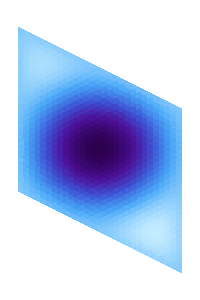

```mathematica
(*Check inversion symmetry,etc, in 1BZ.*)
import=Import[NotebookDirectory[]<>system<>"STMimage.nc","Data"];
kpoints=import[[3]];k1=import[[4]];k2=import[[5]];STMkpoints=import[[6]];
tmp=ListInterpolation[STMkpoints];
size=Dimensions[STMkpoints];
nx=size[[1]];ny=size[[2]];
If[k1>4,res=2,res=1];
ptsx=res nx/k1;ptsy=res ny/k2;
STMkpoints=Table[tmp[ii nx/ptsx,jj ny/ptsy],{ii,ptsx},{jj,ptsy}];
Print["Number of k points along a1: ",k1]
Print["Number of k points along a2: ",k2]
Print["STM images of individual k points:"]
A={{1,-Cos[theta]},{0,1}};
matTransf=Table[{A[[2]].{ii,jj},A[[1]].{ii,jj},STMkpoints[[ii,jj]]},{ii,1,ptsx},{jj,1,ptsy}];
Rotate[ListDensityPlot[Flatten[matTransf,{1,2}],AspectRatio->1+Cos[theta],ColorFunction->"DeepSeaColors",Mesh->False,Frame->False,ImageSize->200,PlotRange->{Min@STMkpoints,Max@STMkpoints}],270 Degree]
```

```mathematica
(*See relaxed geometry of STM device region*)
xyz=import[[7]];atoms=xyz[[;;,1]];g=Gather[atoms];noSpecies=Length[g];
xyz2=Table[0,{ii,Length@xyz},{jj,5}];xyz2[[;;,2;;5]]=xyz;cols=0Range[100];
Table[cols[[ii]]=ElementData[ii,"IconColor"],{ii,40}];
Table[xyz2[[ii]][[1]]=cols[[xyz2[[ii]][[2]]]],{ii,Length[xyz]}];
geom=Table[{xyz2[[ii,1]],Sphere[xyz2[[ii,3;;5]],.4xyz2[[ii,2]]^(1/3.)]},{ii,Length[xyz2]}];
plot=Graphics3D[{Specularity[White,30],geom},Boxed->False,ViewPoint->{5,50,3},ImageSize->300,Lighting->"Neutral",Epilog->Text[Δz:import[[8]]Å,Scaled[{.65,0.5}]]]
```

-Graphics3D-